## Load results, shape descriptor script and trained ConvNet

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\shape descriptors - temporal\\EFD.m";
nNetTrained=Import["C:\\Users\\aliha\\Desktop\\research related\\unet.wlnet"];
```

```mathematica
Block[{file},
Scan[
If[StringMatchQ[#,__~~".mx"],Get[NotebookDirectory[]<>#]]&,
Import@NotebookDirectory[]
]
]
```

## segment masks

```mathematica
segmentMask[stackName_String,maskName_String,opt_:False,ind_:None]:=Module[{img,bx,mask,gray,imgresized,res,results,
resultsm},
img=Import[stackName];
mask=Import[maskName];
bx = Last@@ComponentMeasurements[mask,"BoundingBox"];
gray=Map[ImageAdjust@ImageTrim[#,{First@bx-100,Last@bx+100}]&,img];
If[Cases[ImageDimensions/@gray,{x_,y_}/;(x<160||y<160) ] ≠ {},Abort[]];
imgresized=ImageResize[#,{160,160}]&/@gray;
res=NetDecoder[{"Image"}]@nNetTrained[imgresized,TargetDevice-> "GPU"];
results=Map[FillingTransform@*DeleteSmallComponents@*Binarize]@res;
If[opt,
resultsm=FillingTransform[Binarize@ImageAdjust[MorphologicalPerimeter[#]~Blur~10~Erosion~6~RidgeFilter~1]]&/@results
]; 
If[Head@ind===Integer||Head@ind===List,
resultsm=Fold[ReplacePart[#,#2-> results[[#2]]]&,resultsm,Flatten[ind/.x_Integer:> {x}]];
];
Switch[opt,False,{results,imgresized},_,
{resultsm,imgresized}]
];
```

## Mask 29

```mathematica
(* Mask Extraction *)
```

```mathematica
{resultsm,imgresized}=segmentMask["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\29\\gray 29.tif",
"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\29\\mask 29\\Mask116.tif",True];
```

```mathematica
Rasterize@Grid[Partition[MapThread[Thumbnail[HighlightImage[#1,#2],100]&,{imgresized,resultsm}],10]]
```

-Graphics-

```mathematica
delpos={{37},{52},{62}};
```

```mathematica
efd=EllipticalFourier[#,normalize-> False,order->8,ptsToplot-> 200,locus-> "dcCoefficients"]&/@Delete[resultsm,delpos];
```

```mathematica
descriptors=Map[Cases[#,Except[_Graphics],{3}]&,efd];
```

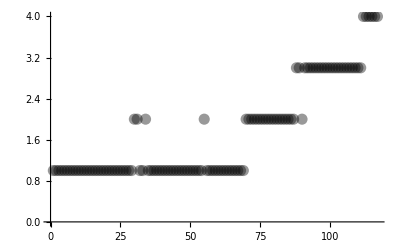

```mathematica
ListPlot[Length/@descriptors,PlotStyle->{PointSize[0.020],XYZColor[0,0,0,0.4]}]
```

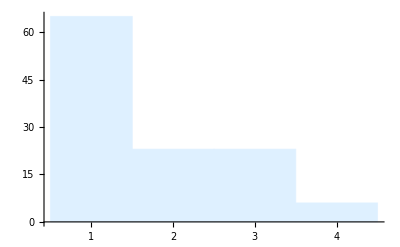

```mathematica
Histogram[Length/@descriptors,ChartStyle->LightBlue]
```

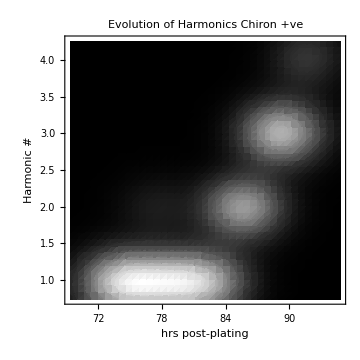

```mathematica
SmoothDensityHistogram[N@Thread[{Delete[Range@120,delpos]/6+72,Length/@descriptors}],ColorFunction->GrayLevel,MeshStyle->{Dashed,Thick,RGBColor[0.10823426242933962, 0.6204150625738422, 0.4678154145759483]},Mesh->5,PlotLabel->Style[#,FontSize->14]&@"Evolution of Harmonics Chiron +ve",FrameLabel->{Style[#,Black,FontSize->14]&@"hrs post-plating",Style[#,Black,FontSize->14]&@"Harmonic #"},
FrameTicksStyle->14,ImageSize->Medium]
```

## Mask 26

```mathematica
{results,imgresized}=segmentMask["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\26\\gray 26.tif",
"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\26\\mask 26\\Mask118.tif"];
```

```mathematica
Rasterize@Grid[Partition[MapThread[Thumbnail[HighlightImage[#1,#2],100]&,{imgresized,results}],10]]
```

-Graphics-

```mathematica
(* mask 26 -> 110 *)
```

```mathematica
efd=EllipticalFourier[#,normalize-> False,order->8,ptsToplot-> 200,locus-> "dcCoefficients"]&/@Delete[results,110];
```

```mathematica
descriptors=Map[Cases[#,Except[_Graphics],{3}]&,efd];
```

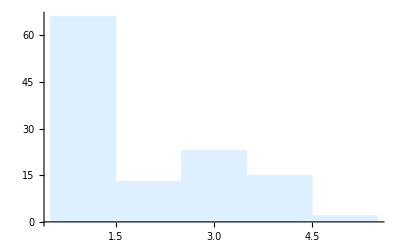

```mathematica
Histogram[Length/@descriptors,ChartStyle->LightBlue]
```

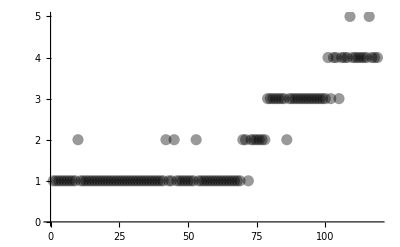

```mathematica
ListPlot[Length/@descriptors,PlotStyle->{PointSize[0.020],XYZColor[0,0,0,0.4]}]
```

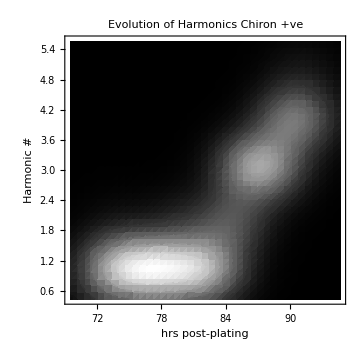

```mathematica
SmoothDensityHistogram[N@Thread[{Delete[Range@120,110]/6+72,Length/@descriptors}],ColorFunction->GrayLevel,MeshStyle->{Dashed,Thick,RGBColor[0.10823426242933962, 0.6204150625738422, 0.4678154145759483]},Mesh->4,PlotLabel->Style[#,FontSize->14]&@"Evolution of Harmonics Chiron +ve",FrameLabel->{Style[#,Black,FontSize->14]&@"hrs post-plating",Style[#,Black,FontSize->14]&@"Harmonic #"},
FrameTicksStyle->14,ImageSize->Medium]
```

## Mask 28

```mathematica
{resultsm,imgresized}=segmentMask["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\28\\gray 28.tif",
"C:\\Users\\aliha\\Desktop\\research related\\raw data\\@polarization prior elongation\\28\\mask 28\\Mask98.tif",True,115];
```

```mathematica
Rasterize@Grid[Partition[MapThread[Thumbnail[HighlightImage[#1,#2],100]&,{imgresized,resultsm}],10]]
```

-Graphics-

```mathematica
efd=EllipticalFourier[#,normalize-> False,order->8,ptsToplot-> 200,locus-> "dcCoefficients"]&/@resultsm;
```

```mathematica
descriptors=Map[Cases[#,Except[_Graphics],{3}]&,efd];
```

```mathematica
len=Length/@descriptors;
```

```mathematica
posdel=Flatten@Position[Take[len,Ceiling[Length[len]/2]],x_/;x>2]
```

{9}

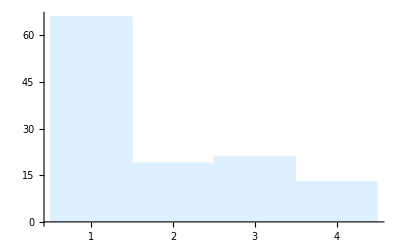

```mathematica
Histogram[Length/@Delete[descriptors,posdel],ChartStyle->LightBlue]
```

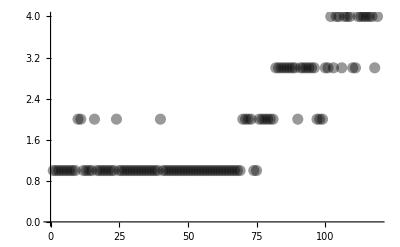

```mathematica
ListPlot[Length/@Delete[descriptors,posdel],PlotStyle->{PointSize[0.020],XYZColor[0,0,0,0.4]}]
```

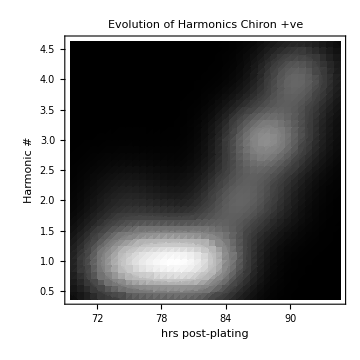

```mathematica
SmoothDensityHistogram[N@Thread[{Delete[Range@120,posdel]/6+72,Delete[Length/@descriptors,posdel]}],ColorFunction->GrayLevel,MeshStyle->{Dashed,Thick,RGBColor[0.10823426242933962, 0.6204150625738422, 0.4678154145759483]},Mesh->3,PlotLabel->Style[#,FontSize->14]&@"Evolution of Harmonics Chiron +ve",FrameLabel->{Style[#,Black,FontSize->14]&@"hrs post-plating",Style[#,Black,FontSize->14]&@"Harmonic #"},
FrameTicksStyle->14,ImageSize->Medium]
```

## Pooled Result

```mathematica
numImages =120;
startPeriod=72 ;(* hours *) 
interval = 6;
endperiod= 94;
```

```mathematica
pooled=Flatten[N@MapThread[Thread[{(Range[numImages]~Delete~#2)/interval+startPeriod,#1}]&,
{Map[Length,saved,{2}],del}],1];
```

```mathematica
SortBy[pooled,First]//SmoothDensityHistogram[#,(* RegionFunction->Function[{x,y,z},z>0.01],*)
ColorFunction->GrayLevel,MeshStyle->{Dashed,Thickness[0.005],RGBColor[0.6607071737450482, 0.3473075964377125, 0.4830795125167045]},Mesh->6,PlotLabel->Style[#,FontSize->14]&@"Evolution of Harmonics Chiron +ve",FrameLabel->{Style[#,Black,FontSize->14]&@"hrs post-plating",Style[#,Black,FontSize->14]&@"Harmonic #"},
FrameTicksStyle->14,ImageSize->Medium]&//Rasterize[#,"Image",ImageResolution->500]&
```

-Graphics-

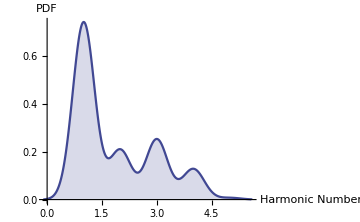

```mathematica
SmoothHistogram[SortBy[pooled,First][[All,2]],PlotStyle->RGBColor[0.25629733545332645, 0.2825694426105453, 0.5753821215001668],Filling->Axis,AxesLabel->{"Harmonic Number","PDF"},AxesStyle->Thick,LabelStyle->Directive[14],ImageSize->Medium]
```

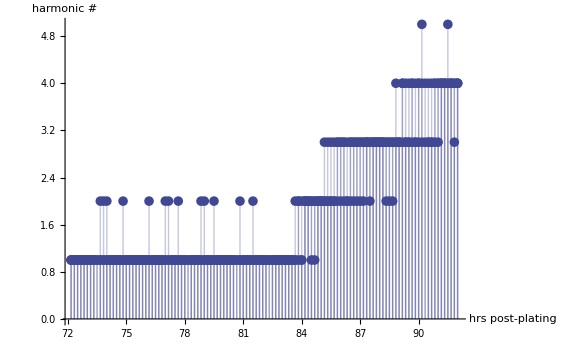

```mathematica
ListPlot[SortBy[pooled,First],PlotStyle->{RGBColor[0.25629733545332645, 0.2825694426105453, 0.5753821215001668],PointSize[0.012]},AxesStyle->Gray,
AxesLabel->{"hrs post-plating","harmonic #"},LabelStyle->Directive[14],Filling->Bottom,
ImageSize->Large]
```

## Tip Dynamics

```mathematica
(* hr -> res *)
```

```mathematica
savedmod=MapThread[Thread[Delete[Range@numImages,#2]->#1]&,{saved,del}];
```

```mathematica
(* convert to dataset *)
```

```mathematica
dataset=Dataset@*Association/@MapAt[<|"L"->#[[1]],"W"->#[[2]],"ψ"->#[[3]],"θ"->#[[4]]|>&/@#&,savedmod,{All,All,2}];
```

### harmonic length and width

```mathematica
Clear@func;
func[x_,y_,z_]:=Thread[{Keys@#,Values@#}]&@Normal@x[[All,y,z]]//DeleteCases[#,{_,Missing[__]}]&//Sort;
```

```mathematica
mag=Block[{subset,lengthfirst,widthfirst,lengthsecond,widthsecond,lengththird,widththird},
Transpose@Map[(
subset=dataset[[#]];
lengthfirst=func[subset,1,"L"];
widthfirst=func[subset,1,"W"];
lengthsecond=func[subset,2,"L"];
widthsecond=func[subset,2,"W"];
lengththird=func[subset,3,"L"];
widththird=func[subset,3,"W"];
{lengthfirst,widthfirst,lengthsecond,widthsecond,lengththird,widththird})&,Range[Length@dataset]
]
];
```

```mathematica
mag= N@MapAt[#/interval+startPeriod&,mag,{All,All,All,1}];
```

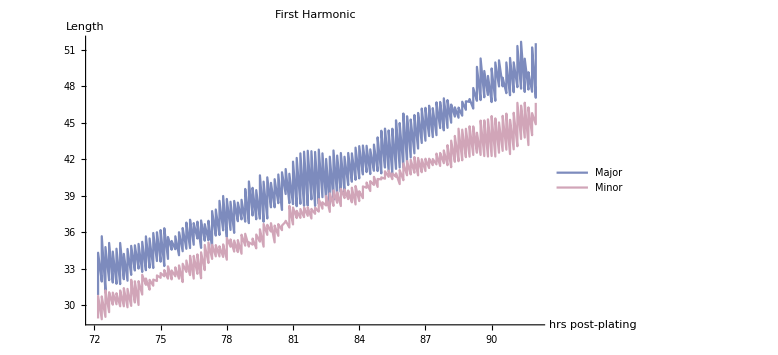

```mathematica
ListPlot[{Sort@Flatten[mag[[1]],1],Sort@Flatten[mag[[2]],1]},PlotStyle->{Lighter@RGBColor[0.23662366005378166, 0.3201359349257917, 0.6098683946554636],RGBColor[0.8198505325329045, 0.6456033728674139, 0.7200310784497016]},Joined->True,AxesLabel->{"hrs post-plating","Length"},LabelStyle->Directive[{Black,14}],PlotLegends->{"Major","Minor"},PlotLabel->"First Harmonic",PlotRange->{{startPeriod,All},Automatic}, ImageSize->Large]
```

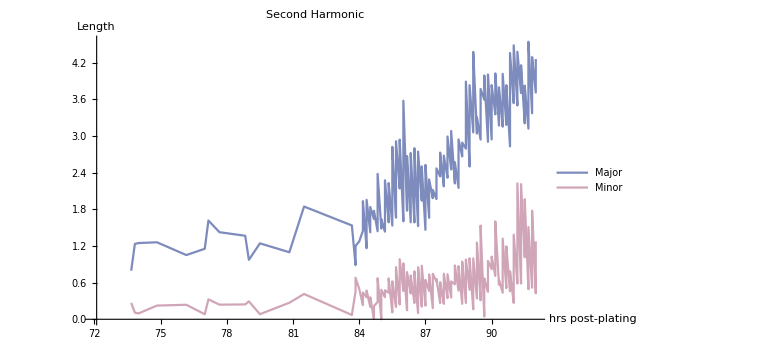

```mathematica
ListPlot[{Sort@Flatten[mag[[3]],1],Sort@Flatten[mag[[4]],1]},PlotStyle->{Lighter@RGBColor[0.23662366005378166, 0.3201359349257917, 0.6098683946554636],RGBColor[0.8198505325329045, 0.6456033728674139, 0.7200310784497016]},Joined->True,
PlotStyle->{Lighter@RGBColor[0.23662366005378166, 0.3201359349257917, 0.6098683946554636],RGBColor[0.8198505325329045, 0.6456033728674139, 0.7200310784497016]},Joined->True,AxesLabel->{"hrs post-plating","Length"},LabelStyle->Directive[{Black,14}],PlotLabel->"Second Harmonic",PlotLegends->{"Major","Minor"},PlotRange->{{startPeriod,All},Automatic},ImageSize->Large]
```

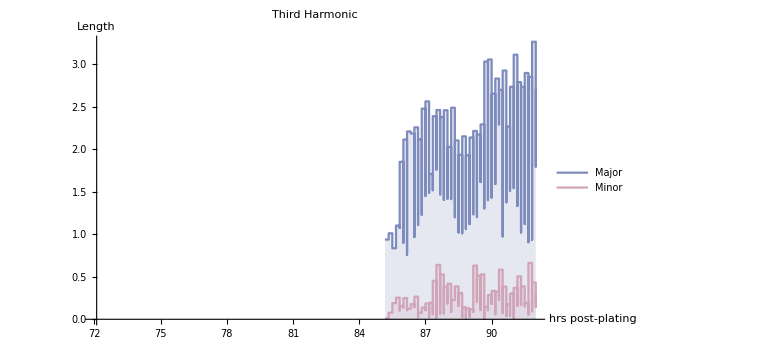

```mathematica
ListStepPlot[{Sort@Flatten[mag[[5]],1],Sort@Flatten[mag[[6]],1]},PlotStyle->{Lighter@RGBColor[0.23662366005378166, 0.3201359349257917, 0.6098683946554636],RGBColor[0.8198505325329045, 0.6456033728674139, 0.7200310784497016]},Joined->True,PlotStyle->{Lighter@RGBColor[0.23662366005378166, 0.3201359349257917, 0.6098683946554636],RGBColor[0.8198505325329045, 0.6456033728674139, 0.7200310784497016]},Joined->True,AxesLabel->{"hrs post-plating","Length"},LabelStyle->Directive[{Black,14}],PlotLegends->{"Major","Minor"},PlotLabel->"Third Harmonic",
PlotRange->{{startPeriod,All},Automatic},Filling->Bottom,ImageSize->Large]
```

### Harmonic Magnitude

```mathematica
With[{lenindices={1,3,5}},
MapThread[
(SmoothDensityHistogram[#, ColorFunction->"LightTemperatureMap",MeshStyle->{Dashed,Thick,Black},Mesh->3,FrameLabel->{Style[#,Black,FontSize->14]&@"hrs post-plating",Style[#,Black,FontSize->14]&@"Area"},
PlotLabel->Style[#2,FontSize->15],FrameTicksStyle->14,PlotRange-> {{startPeriod,endperiod},Automatic},
ImageSize->Medium,AspectRatio->1]//Rasterize[#,"Image",ImageResolution->500]&)&,
{Thread[{Flatten[mag[[#]],1][[All,1]],Flatten[mag[[#]],1][[All,2]]*Flatten[mag[[#+1]],1][[All,2]]}]&/@lenindices,
{"1^st Harmonic","2^nd Harmonic", "3^rd Harmonic"}}
]
]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(* high res plots *)
```